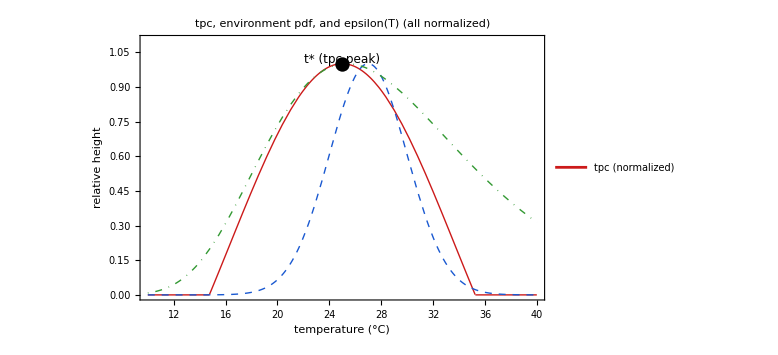

```mathematica
(* 1. HELPER CURVES AND PEAK FINDER ------------------------------------------- *)
(* assumes SuitabilityFunc, ImaxFunc, RespirationFunc are already defined *)

(* normalized lognormal epsilon(T) with target mean; returns 0 for T<=0 *)
EpsilonLogNormalNormalized[meanT_, sigmaLog_] := Module[
  {muLog = Log[meanT] - sigmaLog^2/2., dist, tMode, maxPdf},
  dist = LogNormalDistribution[muLog, sigmaLog];
  tMode = Exp[muLog - sigmaLog^2];
  maxPdf = PDF[dist, tMode];
  Function[{t}, If[t <= 0, 0., PDF[dist, t]/maxPdf]]
];

(* numeric argmax of a univariate function on [tMin, tMax] *)
FindPeakT[fun_, tMin_, tMax_] := Module[{sol},
  sol = NMaximize[{fun[t], tMin <= t <= tMax}, t];
  t /. Last[sol]
];

(* 2. DISPLAY PLOT: TPC, ENV PDF, EPSILON(T) ---------------------------------- *)

(* user knobs *)
rBaseline = 0.8;
tMin = 10; tMax = 40;
suitParams = <|"optT" -> 25, "respBreadth" -> 150, "Rhalf" -> 0.5, "mParams" -> {0.005, 0.002, 0.3}|>;
envSd = 3.;                 (* spread of environmental temps *)
epsShift = 2.;              (* epsilon mean − environment mean (°C) *)
epsSigmaLog = 0.3;          (* log-scale std dev for epsilon *)

(* find tpc peak temperature *)
tpcFun = Function[{t}, SuitabilityFunc[t, rBaseline, suitParams]];
tpcPeakT = FindPeakT[tpcFun, tMin, tMax];

(* pick a baseline ΔT for the overlay figure *)
deltaT = 2.;                                  (* editable *)
envMean = tpcPeakT + deltaT;
epsMean = envMean + epsShift;
epsFun = EpsilonLogNormalNormalized[epsMean, epsSigmaLog];

(* curves, normalized for visualization only *)
tpcCurve = Plot[
  tpcFun[T]/MaxValue[{tpcFun[x], tMin <= x <= tMax}, x],
  {T, tMin, tMax},
  PlotStyle -> {Thick, RGBColor[0.80, 0.10, 0.10]},
  PlotLegends -> Placed[{"tpc (normalized)"}, Above]
];

envCurve = Plot[
  PDF[NormalDistribution[envMean, envSd], T]/PDF[NormalDistribution[envMean, envSd], envMean],
  {T, tMin, tMax},
  PlotStyle -> {Thick, Dashed, RGBColor[0.10, 0.35, 0.82]}
];

epsCurve = Plot[
  epsFun[T],
  {T, tMin, tMax},
  PlotStyle -> {Thick, DotDashed, RGBColor[0.20, 0.60, 0.20]}
];

overlayPlot = Show[
  tpcCurve, envCurve, epsCurve,
  Frame -> True,
  FrameLabel -> {"temperature (°C)", "relative height"},
  PlotLabel -> "tpc, environment pdf, and epsilon(T) (all normalized)",
  ImageSize -> Large,
  Epilog -> {
    Black, PointSize[0.018], Point[{tpcPeakT, 1.0}],
    Text[Style["t* (tpc peak)", 12], {tpcPeakT, 1.02}, {0, -1}]
  },
  PlotRange -> {All, {0, 1.1}}
];

overlayPlot
```

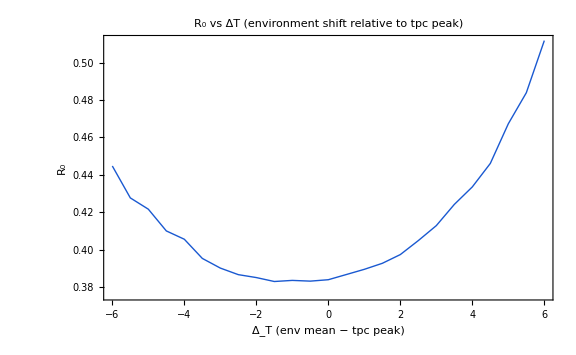

```mathematica
(* 4. BUILD LANDSCAPE FROM ENV AND COMPUTE R₀ ---------------------------------- *)

(* now bin the values appropriately (discretize temps to patches) *)
BuildLandscapeFromEnv[deltaT_, nPatches_, rBase_, suitPars_, envSd_, epsShift_, epsSigmaLog_] := Module[
  {envMeanT, temps, resources, rawSuit, weights, epsVec, epsMeanT},
  envMeanT = tpcPeakT + deltaT;
  temps = RandomVariate[NormalDistribution[envMeanT, envSd], nPatches];
  resources = ConstantArray[rBase, nPatches];
  rawSuit = MapThread[Max[0, SuitabilityFunc[#1, #2, suitPars]] &, {temps, resources}];
  weights = If[Total[rawSuit] > 0, rawSuit/Total[rawSuit], ConstantArray[1./nPatches, nPatches]];
  epsMeanT = envMeanT + epsShift;
  epsVec = EpsilonLogNormalNormalized[epsMeanT, epsSigmaLog] /@ temps;
  <|"weights" -> weights, "epsilon" -> epsVec, "temps" -> temps|>
];

(* expected R0 for I = 1 and S susceptibles *)
R0FromWeights[weights_, epsVec_, s_] := s*Total[(weights^2)*epsVec];

(* 5. SWEEP ΔT AND PLOT R₀(ΔT) ------------------------------------------------ *)

(* now set sweep controls *)
sSus = 2000;                (* total susceptibles S *)
nPatches = 5000;            (* discretization of the landscape *)
deltaGrid = Range[-6, 6, 0.5];

r0Vals = Table[
  Module[{land = BuildLandscapeFromEnv[dT, nPatches, rBaseline, suitParams, envSd, epsShift, epsSigmaLog]},
    R0FromWeights[land["weights"], land["epsilon"], sSus]
  ],
  {dT, deltaGrid}
];

r0Plot = ListLinePlot[
  Transpose[{deltaGrid, r0Vals}],
  Frame -> True,
  FrameLabel -> {"\!\(\*SubscriptBox[\(Δ\), \(T\)]\) (env mean − tpc peak)", "R₀"},
  PlotLabel -> "R₀ vs ΔT (environment shift relative to tpc peak)",
  PlotStyle -> {Thick, RGBColor[0.10, 0.35, 0.82]},
  ImageSize -> Large
];

r0Plot
```